```mathematica
odeSolution= DSolveValue[{m x''[t]==-b x'[t], x[0]==x0, x'[0]==v0}, x[t],t]
```

(ⅇ^(-(b t)/m) (-m v0+ⅇ^((b t)/m) m v0+b ⅇ^((b t)/m) x0))/b

```mathematica
v0=1;x0=1;m=1;b=1;
```

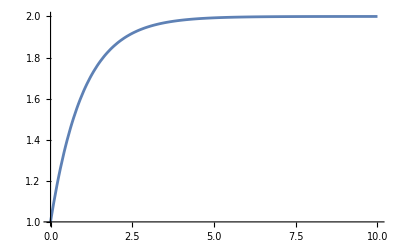

```mathematica
Plot[odeSolution,{t,0,10}, PlotRange->All]
```

```mathematica
velocity = D[odeSolution, t]
```

2-ⅇ^-t (-1+2 ⅇ^t)

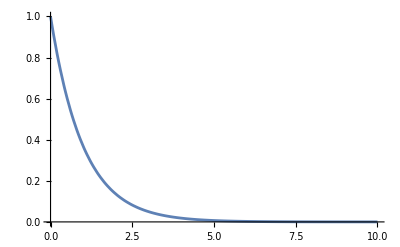

```mathematica
Plot[velocity,{t,0,10}, PlotRange->All]
```